```mathematica
qDis=Table[q,{q,1,10,0.25}];
```

### Data for detectablity

```mathematica
ρA33with220330={Indeterminate,23.038458564089282,13.040824588564574,9.780592738765689,8.179712061349136,7.232600809546135,6.608069659731854,6.165299748168946,5.8357896221762315,5.580425993915651,5.3773830439148504,5.211560016049825,5.074107888963127,4.957756327511841,4.858494944721227,4.772872747541824,4.698306794390208,4.632403011729886,4.574070034125056,4.521907850930879,4.475150630269934,4.432807763439795,4.3944531414514785,4.3595591220479415,4.3276867955266844,4.298228994514979,4.271119634149462,4.246093486545429,4.2229236353909325,4.201414827213578,4.181398156938966,4.162726786046794,4.145272467059742,4.128791049736347,4.113316764117817,4.09876173731509,4.085047997432799};
ρA22with220330={Indeterminate,1.468728728373924,1.4767654929819958,1.486346747434623,1.4961017796273532,1.5054724002146402,1.5143074652587418,1.5223379276430242,1.5299493852386956,1.5367300669125423,1.5431654710077327,1.5488858342506442,1.5543285035612813,1.5590622119283337,1.563567439328801,1.567875577396261,1.5720141892496355,1.5756274025836736,1.5790978903416797,1.5822527977493008,1.5852944853995081,1.5880060638454836,1.590619506462972,1.5931454586173504,1.595593368676826,1.5976609533632322,1.5996581326094836,1.6015914889402498,1.603466919839092,1.6052897241347979,1.6070646760691036,1.608796088965985,1.6104878701076497,1.6119322994189775,1.6133398005860338,1.6147132678412868,1.6160553422560129};
ρA22with220440={1.4679320449139561,1.46757825923925,1.4689851358783383,1.4713264217522615,1.4740392355947556,1.4769010510541167,1.4798670241000988,1.4826713863965346,1.485645840746872,1.4883252579078756,1.4911200193069079,1.4936110284742015,1.4961705311468327,1.4983356384871136,1.5005320818835433,1.5027561632238757,1.5050055839080207,1.5069147037841102,1.5088306239574714,1.5105704275105214,1.5123127874419575,1.5138380081336167,1.515356447449321,1.516868605929094,1.5183751316637175,1.519581901682641,1.5207771308502493,1.5219615276630607,1.5231358270818647,1.5243007765358272,1.5254571254729388,1.5266056176483451,1.5277469855241481,1.5286824755154833,1.5296085603798693,1.5305258611656964,1.5314349766766746};
ρA44with220440={22.698956798065637,29.59126569747201,35.61553374565477,37.1695373703367,34.89506690483921,31.188570142322533,27.534025496574266,24.420419619542784,21.89594849993587,19.871096035432135,18.242982273428876,16.92032238098109,15.833936178343524,14.930347420000325,14.170442690880737,13.524330162052284,12.969403638529846,12.48858739434896,12.068448499263937,11.698704647580335,11.370954836064323,11.07886531559796,10.816877891234766,10.580653585204592,10.366630311018973,10.172318606092366,9.994826057487591,9.832085241533061,9.682348494251956,9.544129291512403,9.416155891844157,9.297334389705531,9.186719050782369,9.083842682113827,8.987641378964458,8.897486672287496,8.812825679039088};
```

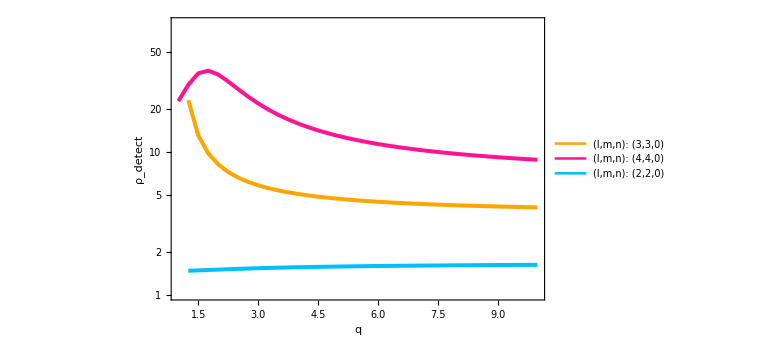

/Users/swetha/Desktop/PlotQtone/aei_rhoDect.pdf

```mathematica
rhoDect=ListLogPlot[{Transpose[{qDis,Abs[ρA33with220330]}],Transpose[{qDis,Abs[ρA44with220440]}],Transpose[{qDis,Abs[ρA22with220330]}]},PlotRange->{{1,10},{1,80}},Frame->True,PlotStyle->{Directive[RGBColor["Orange"],Thickness[0.005]],Directive[RGBColor["DeepPink"],Thickness[0.005]],Directive[RGBColor["DeepSkyBlue"],Thickness[0.005]],Directive[RGBColor["Teal"],Thickness[0.005]],Directive[RGBColor["Crimson"],Thickness[0.005],Dashed],Directive[RGBColor["LimeGreen"],Thickness[0.005],Dashed]},FrameLabel->{HoldForm["q"],HoldForm["ρ_detect "]},LabelStyle->{FontFamily->"Arial",17,GrayLevel[0],Bold},GridLines->{Full,Full},ImageSize->Large,Joined->True,PlotLegends->Placed[LineLegend[{"(l,m,n): (3,3,0)","(l,m,n): (4,4,0)","(l,m,n): (2,2,0)"},LegendLayout->{"Row",3},LegendFunction->(Framed[#,RoundingRadius->5]&)],{0.82,0.82}],ImageSize->Large,Joined->True]
Export["/Users/swetha/Desktop/PlotQtone/aei_rhoDect.pdf",rhoDect,"PDF"]
```

### Data for resolvablity

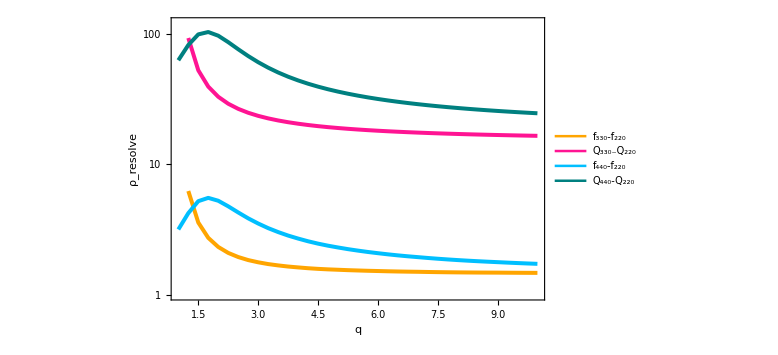

/Users/swetha/Desktop/PlotQtone/aei_rhoRes.pdf

```mathematica
ρResf33with220330={Indeterminate,6.212243859025893,3.5630617367583346,2.7190640992496027,2.315936663093068,2.085009939729325,1.938796825322429,1.837261438098895,1.766869088046557,1.7122329848627895,1.6723750387378096,1.6391725038531142,1.6141534790278103,1.5911642707642695,1.5732095590771793,1.5592930736513315,1.5486722304925922,1.5377052199542087,1.5290365324601611,1.52082481236528,1.5143017277002462,1.5074964469852987,1.5019354713802064,1.4974602348441879,1.493939109556585,1.4890496650684522,1.4849096480615773,1.481437249163855,1.478562553215679,1.4762254621833009,1.4743740381544348,1.4729631706388395,1.4719534965424037,1.4699198269821367,1.4682193065394644,1.466824229305308,1.4657100199901716};

ρResf44with220440={3.1522930612988462,4.203390317600714,5.193181660418003,5.504602935338258,5.232231959101386,4.742708257913104,4.256540328372938,3.8373860888531954,3.502531802219084,3.2286468982104464,3.0118625522817584,2.831578739119157,2.6858960269849743,2.55984692285791,2.4554358642290626,2.3682254388404482,2.294862661429638,2.228110543716229,2.170851955865594,2.1193228739753662,2.0745333809306845,2.0330073135663236,1.9963933715693742,1.963999901167638,1.9352580550704932,1.9067529208162166,1.8810938129745913,1.8579382779085232,1.836996351962922,1.8180210177901344,1.8008006441197475,1.7851529498090264,1.7709201492125752,1.756243952031266,1.742743783366217,1.7303114849192698,1.7188518048544326};

ρResQ33with220330 = {Indeterminate,92.39236816186308,52.26503543298037,39.18519731416485,32.76707915224867,28.974748592413157,26.477484590170725,24.709668823073834,23.39603951852407,22.379250740210175,21.57193759680076,20.91305658179684,20.36756721938023,19.905737529768274,19.512128563711343,19.172910531197655,18.877740346420183,18.61660454757021,18.38561711660826,18.17895488521403,17.993808417583626,17.82594761184437,17.673957438509753,17.535732738259966,17.409522916849518,17.292587727016524,17.184998060564325,17.085696914183327,16.993780107507842,16.908469717869192,16.829092856791693,16.75506457785073,16.68587400877629,16.620372396933263,16.55887872894879,16.501043049041215,16.446554825185597};

ρResQ44with220440 = {62.38056610638248,81.62837704323354,98.48703939123172,102.66817186967123,96.19775332191188,85.87100157297884,75.77724840187281,67.2192704723416,60.301150545939116,54.760004388578274,50.308861270912764,46.69298451925293,43.723704362820925,41.25230623196829,39.17378590586421,37.40640802824638,35.888401450872955,34.571691920312155,33.421061951950676,32.40773848536951,31.509480173033694,30.708173976487387,29.98942068397633,29.34134940692184,28.754210983354646,28.220245874688644,27.732491231552377,27.28528103107743,26.873823781268925,26.494042470447145,26.142447954403423,25.816038010430116,25.51221625867849,25.22914906126504,24.964470212121096,24.716452408307376,24.48357567864481};

rhoResolve=ListLogPlot[{Transpose[{qDis,Abs[ρResf33with220330]}],Transpose[{qDis,Abs[ρResQ33with220330]}],Transpose[{qDis,Abs[ρResf44with220440]}],Transpose[{qDis,Abs[ρResQ44with220440]}]},PlotRange->{{1,10},{1,120}},Frame->True,PlotStyle->{Directive[RGBColor["Orange"],Thickness[0.005]],Directive[RGBColor["DeepPink"],Thickness[0.005]],Directive[RGBColor["DeepSkyBlue"],Thickness[0.005]],Directive[RGBColor["Teal"],Thickness[0.005]],Directive[RGBColor["Crimson"],Thickness[0.005],Dashed],Directive[RGBColor["LimeGreen"],Thickness[0.005],Dashed]},FrameLabel->{HoldForm["q"],HoldForm["ρ_resolve "]},LabelStyle->{FontFamily->"Arial",17,GrayLevel[0],Bold},GridLines->{Full,Full},ImageSize->Large,Joined->True,PlotLegends->Placed[LineLegend[{"f_330-f_220","Q_(330-)Q_220","f_440-f_220", "Q_440-Q_220"},LegendLayout->{"Row",3},LegendFunction->(Framed[#,RoundingRadius->5]&)],{0.70,0.87}],ImageSize->Large,Joined->True]
Export["/Users/swetha/Desktop/PlotQtone/aei_rhoRes.pdf",rhoResolve,"PDF"]
```

### Data for measurability 1%

```mathematica
ρf1percentwith220330={Indeterminate,229.48877171270183,131.79713819503286,100.73319731791769,85.93084031693084,77.47223017925737,72.13510893274191,68.43175770425175,65.88269888626586,63.899692143512105,62.46631455269099,61.266719830842824,60.3722661181125,59.54011546468249,58.89602477603909,58.402940438794005,58.03325033660888,57.64179930917636,57.336474290879295,57.044361942141244,56.815635277173556,56.572127390520116,56.37531532571431,56.21927566998491,56.09909196689867,55.92262583432828,55.77430432152672,55.65106507803575,55.550291158008754,55.469733242798725,55.4074475937044,55.36174614847063,55.331156079279054,55.25930678246215,55.19999073742619,55.152169418067885,55.11492169637916};
ρf1percentwith220440={168.41350947382895,224.6438019407295,277.7366815443269,294.63110613254577,280.27714754466945,254.2372963386169,228.3271128948349,205.95092702336413,188.07954658494484,173.43995221029257,161.85881180687855,152.21414863981693,144.42519482944752,137.6729663820289,132.08250982832323,127.41570494250938,123.49261974476119,119.9152632076987,116.84818598913824,114.08530972284706,111.6848784831127,109.45621770143204,107.49181389263723,105.75447225022002,104.2136022223256,102.68165739163119,101.3029070122878,100.05892149169793,98.93409608605671,97.91513729555736,96.99065600013078,96.15084262571746,95.38720588446526,94.59791529229643,93.87195606386209,93.20350459560339,92.58743222006262};
ρQ1percentwith220330={Indeterminate,3256.6945464396026,1841.7643921298584,1380.3358033134982,1153.8089688777834,1019.8616050734734,931.6003515905951,869.0882123308788,822.6015611323003,786.6154196018375,758.0193165545397,734.6885363178105,715.356847878554,699.0093061407715,685.0658886736351,673.0397578159442,662.5668392301869,653.3177762801067,645.1307465547839,637.8124441766504,631.2515445779455,625.3128332352454,619.9325741940942,615.0367941915433,610.5639815163312,606.4334709924675,602.6314570838267,599.120825458786,595.8698284925746,592.8511523750353,590.0411718055225,587.41934976959,584.9677505419746,582.6546436063085,580.4823571680253,578.4386111751791,576.5125091551569};
ρQ1percentwith220440={3205.6404713400398,4194.256600609541,5059.158650102009,5272.168329419695,4938.21170845502,4406.601339184951,3887.3662234035446,3447.3543789873866,3091.690395286873,2806.935784223225,2578.1834452619237,2392.4332708475467,2239.882306053496,2112.9874093570384,2006.2511381542886,1915.4794842806125,1837.5030058512125,1769.9124863157672,1710.8384177867715,1658.8313792455117,1612.7223227991424,1571.6122005100817,1534.7324012348793,1501.4746504776879,1471.3393978500305,1443.9609461932123,1418.94914961058,1396.0138348341002,1374.9096169004335,1355.4277021755152,1337.3894039166155,1320.6409723760057,1305.049442414973,1290.5376463120926,1276.9671966454243,1264.2496713577395,1252.307262027891}
```

### Data for 5% measurability

```mathematica
ρf5percentwith220330={Indeterminate,45.89775434254036,26.35942763900657,20.146639463583536,17.186168063386166,15.494446035851473,14.427021786548384,13.686351540850351,13.176539777253172,12.77993842870242,12.493262910538196,12.253343966168565,12.074453223622497,11.908023092936501,11.779204955207819,11.680588087758803,11.606650067321777,11.528359861835272,11.467294858175858,11.408872388428248,11.363127055434713,11.314425478104022,11.275063065142863,11.24385513399698,11.219818393379736,11.184525166865654,11.154860864305345,11.130213015607149,11.110058231601752,11.093946648559745,11.081489518740883,11.072349229694128,11.06623121585581,11.051861356492433,11.039998147485239,11.030433883613576,11.022984339275833};
```

```mathematica
ρf5percentwith220440={33.6827018947658,44.928760388145896,55.547336308865376,58.92622122650914,56.05542950893389,50.84745926772337,45.665422578966975,41.19018540467282,37.615909316988976,34.68799044205851,32.37176236137571,30.442829727963385,28.88503896588951,27.534593276405783,26.416501965664647,25.483140988501876,24.698523948952236,23.983052641539743,23.369637197827647,22.81706194456941,22.336975696622538,21.891243540286407,21.498362778527447,21.150894450044007,20.84272044446512,20.53633147832624,20.260581402457564,20.01178429833959,19.786819217211338,19.583027459111474,19.39813120002616,19.230168525143494,19.077441176893053,18.91958305845929,18.77439121277242,18.64070091912068,18.517486444012526};
ρQ5percentwith220330={Indeterminate,651.3389092879205,368.35287842597165,276.0671606626996,230.76179377555667,203.97232101469464,186.32007031811898,173.81764246617578,164.52031222646005,157.3230839203675,151.60386331090794,146.93770726356212,143.07136957571083,139.80186122815428,137.013177734727,134.60795156318883,132.51336784603737,130.66355525602134,129.02614931095678,127.5624888353301,126.25030891558907,125.06256664704908,123.98651483881882,123.00735883830866,122.11279630326624,121.28669419849348,120.52629141676537,119.8241650917572,119.1739656985149,118.57023047500707,118.00823436110448,117.48386995391799,116.99355010839491,116.53092872126173,116.09647143360507,115.6877222350358,115.30250183103138};
ρQ5percentwith220440={641.128094268008,838.8513201219081,1011.8317300204017,1054.433665883939,987.642341691004,881.3202678369902,777.4732446807088,689.4708757974772,618.3380790573747,561.387156844645,515.6366890523847,478.48665416950934,447.97646121069926,422.59748187140775,401.25022763085775,383.0958968561224,367.50060117024253,353.98249726315345,342.16768355735434,331.7662758491023,322.5444645598285,314.32244010201634,306.9464802469759,300.29493009553755,294.2678795700061,288.79218923864244,283.78982992211604,279.2027669668201,274.9819233800867,271.085540435103,267.4778807833231,264.12819447520116,261.00988848299465,258.10752926241855,255.39343932908486,252.84993427154788,250.46145240557823};
```

### Data for 10% measurability

```mathematica
ρf10percentwith220330={Indeterminate,22.94887717127018,13.179713819503284,10.073319731791768,8.593084031693083,7.747223017925736,7.213510893274191,6.8431757704251766,6.588269888626586,6.38996921435121,6.246631455269098,6.126671983084282,6.037226611811248,5.954011546468251,5.889602477603908,5.8402940438794015,5.803325033660888,5.764179930917638,5.73364742908793,5.704436194214124,5.681563527717357,5.657212739052012,5.6375315325714315,5.62192756699849,5.609909196689868,5.592262583432827,5.577430432152672,5.565106507803574,5.555029115800876,5.546973324279873,5.54074475937044,5.536174614847064,5.533115607927905,5.525930678246216,5.5199990737426194,5.515216941806787,5.5114921696379175};
```

```mathematica
ρf10percentwith220440={16.8413509473829,22.464380194072945,27.773668154432688,29.46311061325457,28.027714754466945,25.423729633861686,22.832711289483488,20.595092702336416,18.807954658494488,17.343995221029257,16.185881180687854,15.221414863981689,14.442519482944755,13.767296638202891,13.208250982832324,12.741570494250938,12.349261974476118,11.991526320769871,11.684818598913823,11.408530972284705,11.168487848311269,10.945621770143203,10.749181389263725,10.575447225022003,10.42136022223256,10.268165739163122,10.130290701228782,10.005892149169796,9.893409608605669,9.791513729555737,9.69906560001308,9.615084262571745,9.538720588446527,9.459791529229642,9.38719560638621,9.32035045956034,9.258743222006263};
ρQ10percentwith220330={Indeterminate,325.6694546439603,184.17643921298583,138.03358033134978,115.38089688777833,101.98616050734732,93.16003515905949,86.9088212330879,82.26015611323002,78.66154196018375,75.80193165545398,73.46885363178106,71.5356847878554,69.90093061407714,68.5065888673635,67.30397578159442,66.25668392301868,65.33177762801067,64.51307465547839,63.78124441766505,63.12515445779455,62.53128332352454,61.993257419409424,61.503679419154324,61.05639815163312,60.64334709924674,60.263145708382694,59.91208254587859,59.58698284925745,59.28511523750353,59.00411718055224,58.741934976959,58.49677505419746,58.265464360630865,58.04823571680253,57.84386111751789,57.651250915515696};
ρQ10percentwith220440={320.56404713400394,419.42566006095404,505.91586501020083,527.2168329419694,493.821170845502,440.6601339184951,388.7366223403544,344.7354378987386,309.16903952868734,280.6935784223225,257.81834452619233,239.24332708475467,223.98823060534963,211.29874093570388,200.62511381542888,191.54794842806118,183.75030058512127,176.99124863157672,171.08384177867717,165.88313792455116,161.27223227991425,157.16122005100817,153.47324012348795,150.14746504776875,147.13393978500304,144.39609461932122,141.89491496105802,139.60138348341005,137.49096169004335,135.5427702175515,133.73894039166154,132.06409723760058,130.50494424149733,129.0537646312093,127.69671966454241,126.42496713577394,125.23072620278911};
```

### Combined = Detect+Resolve+Measure

#### At 1% level

```mathematica
f1percentWith330=MapThread[Max,{ρf1percentwith220330,ρResf33with220330,ρA33with220330}];
f1percentWith440=MapThread[Max,{ρf1percentwith220440,ρResf44with220440,ρA44with220440}];
Q1percentWith330=MapThread[Max,{ρQ1percentwith220330,ρResQ33with220330,ρA33with220330}];
Q1percentWith440=MapThread[Max,{ρQ1percentwith220440,ρResQ44with220440,ρA44with220440}];
```

#### At 5% level

```mathematica
f5percentWith330=MapThread[Max,{ρf5percentwith220330,ρResf33with220330,ρA33with220330}];
f5percentWith440=MapThread[Max,{ρf5percentwith220440,ρResf44with220440,ρA44with220440}];
Q5percentWith330=MapThread[Max,{ρQ5percentwith220330,ρResQ33with220330,ρA33with220330}];
Q5percentWith440=MapThread[Max,{ρQ5percentwith220440,ρResQ44with220440,ρA44with220440}];
```

#### At 10% level

```mathematica
f10percentWith330=MapThread[Max,{ρf10percentwith220330,ρResf33with220330,ρA33with220330}];
f10percentWith440=MapThread[Max,{ρf10percentwith220440,ρResf44with220440,ρA44with220440}];
Q10percentWith330=MapThread[Max,{ρQ10percentwith220330,ρResQ33with220330,ρA33with220330}];
Q10percentWith440=MapThread[Max,{ρQ10percentwith220440,ρResQ44with220440,ρA44with220440}];
```

```mathematica
r1=ListLogPlot[{f1percentWith330,f1percentWith440,f5percentWith330,f5percentWith440,f10percentWith330,f10percentWith440},PlotRange->{{1,10},{4,800}},Frame->True,LabelStyle->{17,GrayLevel[0]},PlotStyle->{Directive[colors[[1]],Dashed,Thick],Directive[colors[[2]],DotDashed,Thick],Directive[colors[[3]],Dotted,Thick],Directive[colors[[1]],Thick],Directive[colors[[2]],Thick],Directive[colors[[3]],Thick]},FrameStyle->Directive[Black,18],LabelStyle->Directive[Black,18],FrameLabel->{"q","ρ_min for f_sub"},GridLines->Automatic,Frame->True,Joined->True,AspectRatio->Full,PlotLegends->Placed[LineLegend[{{"33 at 1%","44 at 1%","33 at 5%",None,None,None}},LegendLayout->{"Column",6},LegendMarkerSize->21,Spacings->1],{0.5,1.00001}]];
r2=ListLogPlot[{Q1percentWith330,Q1percentWith440,Q5percentWith330,Q5percentWith440,Q10percentWith330,Q10percentWith440},PlotRange->{{1,10},{40,1200}},LabelStyle->{17,GrayLevel[0]},PlotStyle->{Directive[colors[[1]],Dashed,Thick],Directive[colors[[2]],DotDashed,Thick],Directive[colors[[3]],Dotted,Thick],Directive[colors[[1]],Thick],Directive[colors[[2]],Thick],Directive[colors[[3]],Thick]},FrameStyle->Directive[Black,18],LabelStyle->Directive[Black,18],FrameLabel->{"q","ρ_min for Q_sub"},GridLines->Automatic,Frame->True,Joined->True,AspectRatio->Full,PlotLegends->Placed[LineLegend[{{None,None,None,"44 at 5%","33 at 10%","44 at 10%"}},LegendLayout->{"Column",6},LegendMarkerSize->21,Spacings->1],{0.5,1.00001}]];

g1=GraphicsRow[{r1,r2},Alignment->Center,ImageSize->{1200,407},AspectRatio->Full]
```

Part::partd: Part specification colors⟦1⟧ is longer than depth of object.

Part::partd: Part specification colors⟦2⟧ is longer than depth of object.

Part::partd: Part specification colors⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification colors⟦1⟧ is longer than depth of object.

Part::partd: Part specification colors⟦2⟧ is longer than depth of object.

Part::partd: Part specification colors⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-